Confronting neutrino mixing schemes with correlations of oscillation data           
Package and Example nb file                                                        
Cite as:  
arXiv:
J. Gluza, B. Karmakar, S. Zieba

## NuFIT Data Import

```mathematica
SetDirectory[NotebookDirectory[]];
```

NuFIT data files 
http://www.nu-fit.org
https://doi.org/10.1007/JHEP12(2024)216
arXiv:2410.05380[hep-ph]

NuFIT v6.0 and v6.1 datasets are included in datasets folder.
Use one version at a time.
To use a custom dataset, download and extract it into the datasets folder, then update the filenames below in the notebook (Import[“...”, “Table”]). 

NuFIT v6.0 
http://www.nu-fit.org/?q=node/294#label85

NuFIT v6.1 
http://www.nu-fit.org/?q=node/309#label85

```mathematica
(*nufitdatatabno=Import["./datasets/v60.release-TByes-NO.txt","Table"];
nufitdatatabio=Import["./datasets/v60.release-TByes-IO.txt","Table"];*)
nufitdatatabno=Import["./datasets/v61.release-TByes-NO.txt","Table"];
nufitdatatabio=Import["./datasets/v61.release-TByes-IO.txt","Table"];
```

## NuFIT Data Preprocessing

### Extracting Available Data for Parameter Combinations

Oscillation parameter data are extracted for available parameter combinations from a single NuFIT data file. The file contains one-,two-,and three-dimensional datasets.

```mathematica
nufitdatapos=Append[(DeleteDuplicates[Position[nufitdatatabno,_?StringQ][[;;,1]]])[[2;;]],Length[nufitdatatabno]+1];
```

```mathematica
nufitcoreln=StringSplit[(nufitdatatabno[[#]]  & /@ nufitdatapos[[;;-2]] )[[;;,2]],"/"];
```

```mathematica
nufitdatalno=nufitdatatabno[[nufitdatapos[[#]]+1;;nufitdatapos[[#+1]]-2]] & /@ Range[Length[nufitdatapos]-1];
nufitdatalio=nufitdatatabio[[nufitdatapos[[#]]+1;;nufitdatapos[[#+1]]-2]] & /@ Range[Length[nufitdatapos]-1];
```

```mathematica
nufitadatano=AssociationThread[nufitcoreln->nufitdatalno];
nufitadataio=AssociationThread[nufitcoreln->nufitdatalio];
```

### Adapting data representation to the chosen convention

In NuFIT datasets δ_CP (DCP) is given in -180° to +180° range and Δm_21^2 (DMS)is given as Log(Δm_21^2). 
For the details refer to: http://www.nu-fit.org/sites/default/files/v61.release-notes.pdf

Applied transformations :     

DCP : (-180, 180) -> (0, 360) 
	  DMS : Log(DMS) -> DMS/10^-5   

 The convention is:

T13 : sin^2 θ_13 / 10^-2,
     T12 : sin^2 θ_12 / 10^-1,
     T23 : sin^2 θ_23 / 10^-1,
     DCP : δ_CP / °,
     DMS : Δm_21^2 / 10^-5 eV^2,
     DMA : Δm_(3l)^2 / 10^-3 eV^2.

     χ^2 values provided by NuFIT are minimized in respect to NO. 
In this approach the data are minimized independently for NO and IO.

### Adapting data representation to the chosen convention and minimizing with respect to mass ordering

```mathematica
rescaleparamfunc[paramnamevar_,paramvaluevar_]:=
Which[
paramnamevar=="DCP",If[paramvaluevar<0,paramvaluevar+360,paramvaluevar],
paramnamevar=="DMS",10^(paramvaluevar+5),
True, paramvaluevar
]
```

finding NuFIT minimum values of χ^2 - to minimize the data

```mathematica
assocnufitminshiftno =Association[#->Min[nufitadatano[#][[;;,Length[#]+1]]] & /@ Keys[nufitadatano]];
assocnufitminshiftio =Association[#->Min[nufitadataio[#][[;;,Length[#]+1]]] & /@ Keys[nufitadataio]];
```

```mathematica
rescaledatafuncminimized[assocdatavar_,assocdatashift_]:=Association[#->Which[ 
Length[#]==3, Join[DeleteDuplicates[Cases[assocdatavar[#],{val1_,val2_,val3_,chival_}-> {rescaleparamfunc@@@{{#[[1]],val1},{#[[2]],val2},{#[[3]],val3}},chival-assocdatashift[#]}]],
Cases[assocdatavar[#],{val1_,val2_,val3_,chival_}/; (#[[1]]=="DCP" && val1==0)-> {rescaleparamfunc@@@{{#[[1]],val1+360},{#[[2]],val2},{#[[3]],val3}},chival-assocdatashift[#]}],
Cases[assocdatavar[#],{val1_,val2_,val3_,chival_}/; (#[[2]]=="DCP" && val2==0)-> {rescaleparamfunc@@@{{#[[1]],val1},{#[[2]],val2+360},{#[[3]],val3}},chival-assocdatashift[#]}],
Cases[assocdatavar[#],{val1_,val2_,val3_,chival_}/; (#[[3]]=="DCP" && val3==0)-> {rescaleparamfunc@@@{{#[[1]],val1},{#[[2]],val2},{#[[3]],val3+360}},chival-assocdatashift[#]}]
],
Length[#]==2, Join[DeleteDuplicates[Cases[assocdatavar[#],{val1_,val2_,chival_}-> {rescaleparamfunc@@@{{#[[1]],val1},{#[[2]],val2}},chival-assocdatashift[#]}]],
Cases[assocdatavar[#],{val1_,val2_,chival_}/; (#[[1]]=="DCP" && val1==0)-> {rescaleparamfunc@@@{{#[[1]],val1+360},{#[[2]],val2}},chival-assocdatashift[#]}],
Cases[assocdatavar[#],{val1_,val2_,chival_}/; (#[[2]]=="DCP" && val2==0)-> {rescaleparamfunc@@@{{#[[1]],val1},{#[[2]],val2+360}},chival-assocdatashift[#]}]
],
Length[#]==1, Join[DeleteDuplicates[Cases[assocdatavar[#],{val1_,chival_}-> {rescaleparamfunc@@@{{#[[1]],val1}},chival-assocdatashift[#]}]],
Cases[assocdatavar[#],{val1_,chival_}/; (SubsetQ[#,{"DCP"}] && val1==0)-> {rescaleparamfunc@@@{{#[[1]],val1+360}},chival-assocdatashift[#]}]],
True, assocdatavar[#]
]
 & /@ Keys[assocdatavar]];
```

NuFIT data adapted and minimized

```mathematica
nufitadatanorm=rescaledatafuncminimized[nufitadatano,assocnufitminshiftno];
nufitadataiorm=rescaledatafuncminimized[nufitadataio,assocnufitminshiftio];
```

## Data Interpolation and Sample Function Calls

Interpolation of the data

```mathematica
nufitfintno=Association[#-> Interpolation[nufitadatanorm[#]] & /@ nufitcoreln];
nufitfintio=Association[#-> Interpolation[nufitadataiorm[#]] & /@ nufitcoreln];
```

List of NuFIT correlations

```mathematica
nufitcoreln // Grid
```

T23 | DMA | DCP
T13 | T12 | 
T13 | DMS | 
T12 | DMS | 
T13 | T23 | 
T13 | DMA | 
T23 | DMA | 
T13 | DCP | 
T23 | DCP | 
DMA | DCP | 
T12 | T23 | 
T12 | DCP | 
T12 | DMA | 
DMS | T23 | 
DMS | DCP | 
DMS | DMA | 
T13 |  | 
T12 |  | 
T23 |  | 
DCP |  | 
DMS |  | 
DMA |  |

```mathematica
nufitcoreln
```

{{T23,DMA,DCP},{T13,T12},{T13,DMS},{T12,DMS},{T13,T23},{T13,DMA},{T23,DMA},{T13,DCP},{T23,DCP},{DMA,DCP},{T12,T23},{T12,DCP},{T12,DMA},{DMS,T23},{DMS,DCP},{DMS,DMA},{T13},{T12},{T23},{DCP},{DMS},{DMA}}

Examples - the result is interpolated χ^2 - NO

```mathematica
nufitfintno[{"DCP"}][170]
```

1.33731

```mathematica
nufitfintno[{"T23","DCP"}][0.45,170]
```

9.51968

```mathematica
nufitfintno[{"T23","DMA","DCP"}][0.45,2.5,170]
```

10.6913

Examples - the result is interpolated χ^2 - minimized - IO

```mathematica
nufitfintio[{"DCP"}][170]
```

21.3494

```mathematica
nufitfintio[{"T23","DCP"}][0.55,170]
```

21.6764

```mathematica
nufitfintio[{"T23","DMA","DCP"}][0.55,-2.5,170]
```

23.535

## Creating 1D, 2D and 3D plots

1D plots - NO

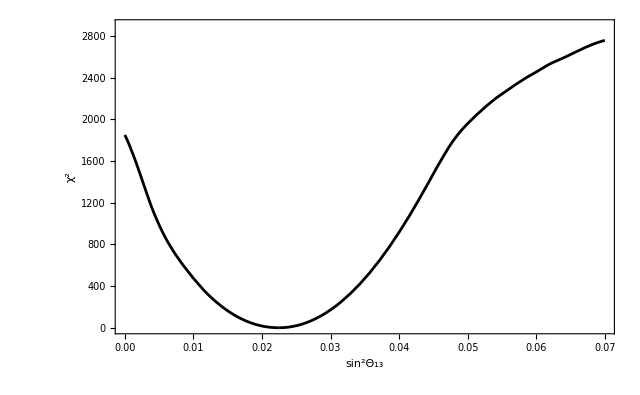

```mathematica
Plot[
nufitfintno[{"T13"}][t13],{t13,0,0.07},
PlotRange->{{0,0.07},{0,2900}},
Frame->True,
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
FrameLabel->{"sin^2Θ_13","χ^2"},
PlotStyle->Black,
ImageSize->640
]
```

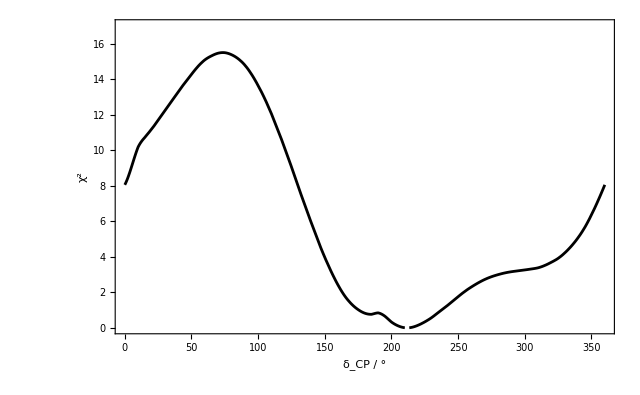

```mathematica
Plot[
nufitfintno[{"DCP"}][dcp],{dcp,0,360},
PlotRange->{{0,360},{0,17}},
Frame->True,
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
FrameLabel->{"δ_CP / °","χ^2"},
PlotStyle->Black,
ImageSize->640
]
```

1 D plot - IO

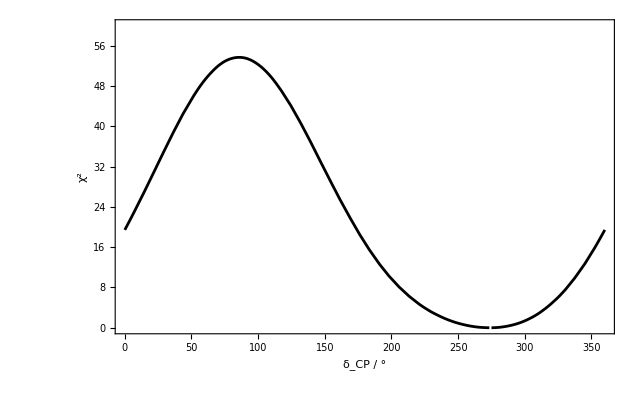

```mathematica
Plot[
nufitfintio[{"DCP"}][dcp],{dcp,0,360},
PlotRange->{{0,360},{0,60}},
Frame->True,
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
FrameLabel->{"δ_CP / °","χ^2"},
PlotStyle->Black,
ImageSize->640
]
```

2D contour plot - NO

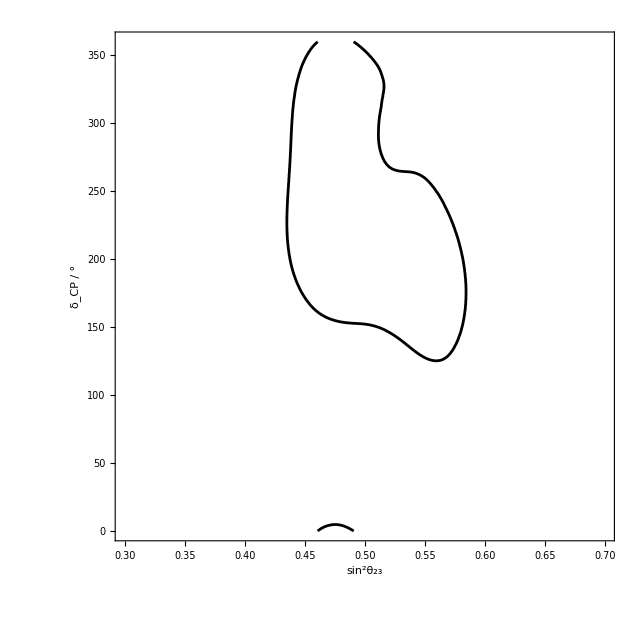

```mathematica
ContourPlot[
nufitfintno[{"T23","DCP"}][t23,dcp]==9,{t23,0.3,0.7},{dcp, 0,360},
PlotRange->{{0.3,0.7},{0,360}},
ContourStyle->Black,
Frame->True,
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
FrameLabel->{"sin^2θ_23","δ_CP / °"},
ImageSize->640,
PlotPoints->50
]
```

2 D contour plot - IO

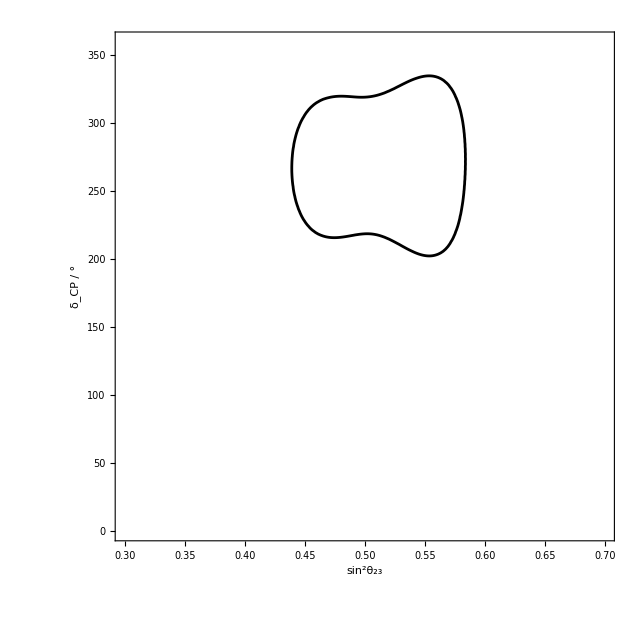

```mathematica
ContourPlot[
nufitfintio[{"T23","DCP"}][t23,dcp]==9,{t23,0.3,0.7},{dcp, 0,360},
PlotRange->{{0.3,0.7},{0,360}},
ContourStyle->Black,
Frame->True,
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
FrameLabel->{"sin^2θ_23","δ_CP / °"},
ImageSize->640,
PlotPoints->50
]
```

3 D contour plot - NO

```mathematica
ContourPlot3D[
nufitfintno[{"T23","DMA","DCP"}][t23,dma,dcp]==9,{t23,0.3,0.7},{dma,2.3,2.7},{dcp,0,360},
ContourStyle->{Black, Opacity[0.1]},
AxesLabel->{"sin^2θ_23","Δm_31^2 / 10^-3 eV^2","δ_CP / °"},
AxesStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640,
PlotPoints->10
]
```

-Graphics3D-

3 D contour plot - IO

```mathematica
ContourPlot3D[
nufitfintio[{"T23","DMA","DCP"}][t23,dma,dcp]==9,{t23,0.3,0.7},{dma,-2.7,-2.3},{dcp,0,360},
ContourStyle->{Black, Opacity[0.1]},
AxesLabel->{"sin^2θ_23","Δm_31^2 / 10^-3 eV^2","δ_CP / °"},
AxesStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640,
PlotPoints->10
]
```

-Graphics3D-

## Creating (χ̃)^2 - Extended Multivariable χ^2 Function and Examples

Extending interpolated χ^2 function to any set of variables (≥2 and ≤6)

```mathematica
chisqtilde[paramvarlist__,variablelist__,nufitchiassocvar_]:=
Max[#1@@#2 & @@@ 
Join[
Thread[{(nufitchiassocvar/@Cases[Keys[nufitchiassocvar],{val1_,val2_} /;SubsetQ[paramvarlist,{val1,val2}]]),
Cases[Keys[nufitchiassocvar],{val1_,val2_} /;SubsetQ[paramvarlist,{val1,val2}]]/.Thread[paramvarlist->variablelist]}],
Thread[{(nufitchiassocvar/@Cases[Keys[nufitchiassocvar],{val1_,val2_,val3_} /;SubsetQ[paramvarlist,{val1,val2,val3}]]),
Cases[Keys[nufitchiassocvar],{val1_,val2_,val3_} /;SubsetQ[paramvarlist,{val1,val2,val3}]]/.Thread[paramvarlist->variablelist]}]
]
];
```

Examples NO

```mathematica
chisqtilde[{"T23","T13"},{s23sq,s13sq},nufitfintno]
```

InterpolatingFunction[…][s13sq,s23sq]

```mathematica
chisqtilde[{"T23","T13","DMA"},{s23sq,s13sq,dma},nufitfintno]
```

Max[InterpolatingFunction[…][s13sq,dma],InterpolatingFunction[…][s13sq,s23sq],InterpolatingFunction[…][s23sq,dma]]

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{s23sq,s13sq,dcp, dma},nufitfintno]
```

Max[InterpolatingFunction[…][s13sq,dcp],InterpolatingFunction[…][s13sq,dma],InterpolatingFunction[…][s13sq,s23sq],InterpolatingFunction[…][dma,dcp],InterpolatingFunction[…][s23sq,dcp],InterpolatingFunction[…][s23sq,dma],InterpolatingFunction[{{0.25, 0.75}, {0.2, 7.}, {0., 360.}}, <>][s23sq,dma,dcp]]

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{0.47,0.0221,212, 2.513},nufitfintno]
```

0.40971

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{0.4,0.0221,212, 2.513},nufitfintno]
```

51.625

Examples IO

```mathematica
chisqtilde[{"T23","T13"},{s23sq,s13sq},nufitfintio]
```

InterpolatingFunction[…][s13sq,s23sq]

```mathematica
chisqtilde[{"T23","T13","DMA"},{s23sq,s13sq,dma},nufitfintio]
```

Max[InterpolatingFunction[…][s13sq,dma],InterpolatingFunction[…][s13sq,s23sq],InterpolatingFunction[…][s23sq,dma]]

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{s23sq,s13sq,dcp, dma},nufitfintio]
```

Max[InterpolatingFunction[…][dma,dcp],InterpolatingFunction[…][s13sq,dma],InterpolatingFunction[…][s13sq,dcp],InterpolatingFunction[…][s13sq,s23sq],InterpolatingFunction[…][s23sq,dma],InterpolatingFunction[…][s23sq,dcp],InterpolatingFunction[{{0.25, 0.75}, {-7., -0.2}, {0., 360.}}, <>][s23sq,dma,dcp]]

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{0.55,0.0223,274, -2.484},nufitfintio]
```

0.331792

```mathematica
chisqtilde[{"T23","T13","DCP","DMA"},{0.55,0.0123,274, -2.484},nufitfintio]
```

339.023

## TM_1 Relations and Sample Plots

TM_1 mixing scheme relations

```mathematica
cosdcptm1[s23sqvar_,s13sqvar_]:=(1-5s13var^2)(2 s23var^2-1)/(4s13var*s23var*(2(1-3s13var^2)(1-s23var^2))^(1/2)) /. {s23var->s23sqvar^(1/2),s13var->s13sqvar^(1/2)};
s12sqtm1[s13sqvar_]:=(1-3s13sqvar)/(3-3s13sqvar);
```

TM_1 example, (χ̃)^2,  2D plane, NO

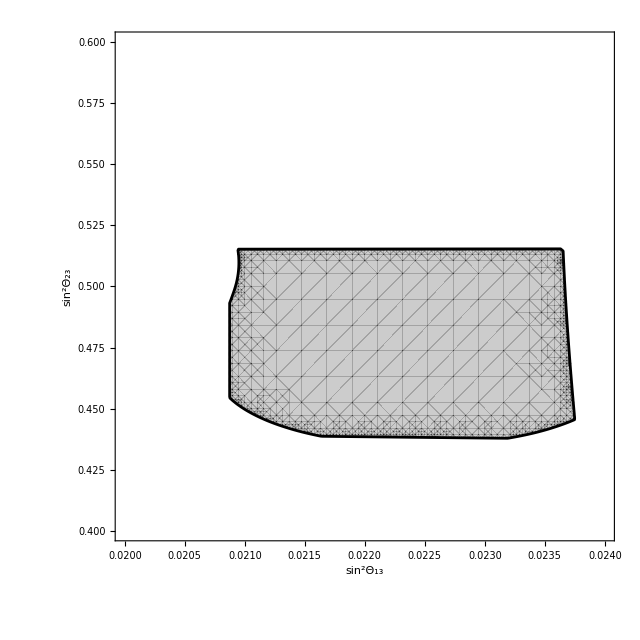

```mathematica
RegionPlot[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno]
] ≤ 9,
{s13sq,0.02,0.024},
{s23sq,0.4,0.6},
PlotPoints->20,
MaxRecursion->5,
FrameLabel->{"sin^2Θ_13","sin^2Θ_23"},
BoundaryStyle-> Black, 
PlotStyle->Directive[Black,Opacity[0.2]],
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```

TM_1 example, (χ̃)^2, 2D plane, IO

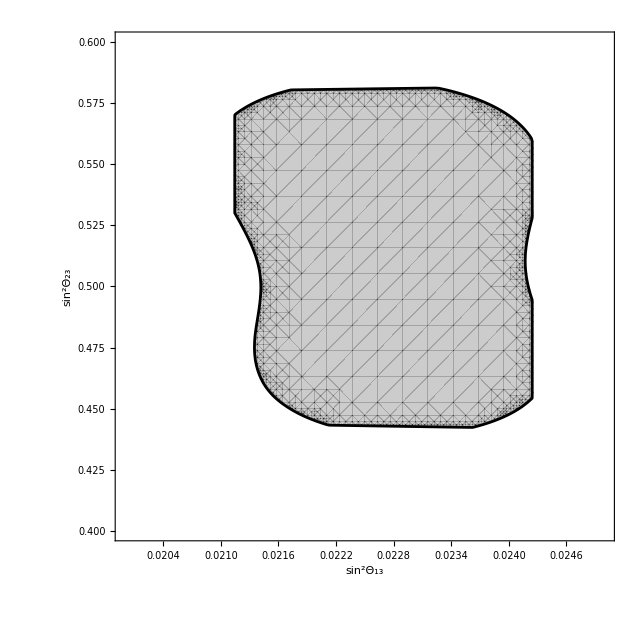

```mathematica
RegionPlot[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio]
] ≤ 9,
{s13sq,0.02,0.025},
{s23sq,0.4,0.6},
PlotPoints->20,
MaxRecursion->5,
FrameLabel->{"sin^2Θ_13","sin^2Θ_23"},
BoundaryStyle-> Black, 
PlotStyle->Directive[Black,Opacity[0.2]],
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```

TM_1 examples, (χ̃)^2, 1D profiles,  NO

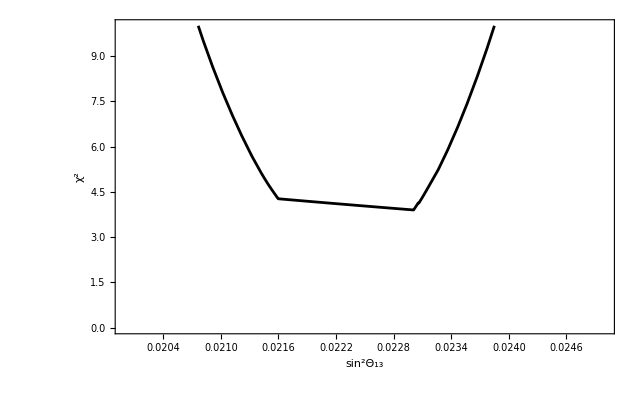

```mathematica
Plot[
Min[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno]
] /. s23sq-> # &/@ Range[.4,.6,.0025]
]
,
{s13sq,0.02,0.025},
Frame->True,
PlotRange->{{0.02,0.025},{0,10}},
PlotStyle->Black,
FrameLabel->{"sin^2Θ_13","χ^2"},
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```

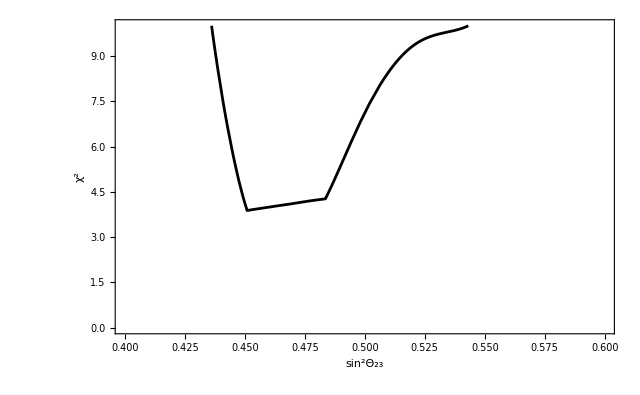

```mathematica
Plot[
Min[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintno]
] /. s13sq-> # &/@ Range[0.02,0.025,.00005]
]
,
{s23sq,0.4,0.6},
Frame->True,
PlotRange->{{0.4,0.6},{0,10}},
PlotStyle->Black,
FrameLabel->{"sin^2Θ_23","χ^2"},
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```

TM_1 examples, (χ̃)^2, 1D profiles, IO

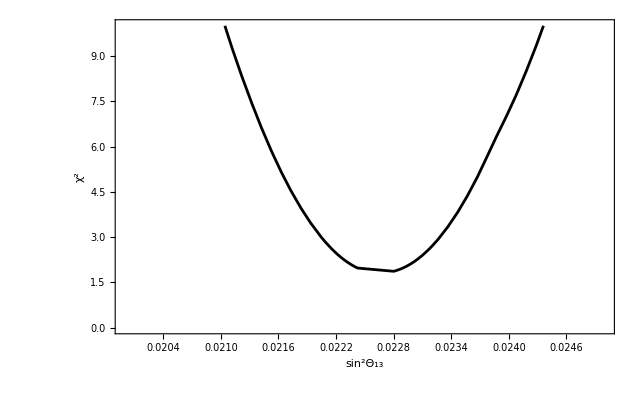

```mathematica
Plot[
Min[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio]
] /. s23sq-> # &/@ Range[0.4,0.6,0.0025]
]
,
{s13sq,0.02,0.025},
Frame->True,
PlotRange->{{0.02,0.025},{0,10}},
PlotStyle->Black,
FrameLabel->{"sin^2Θ_13","χ^2"},
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```

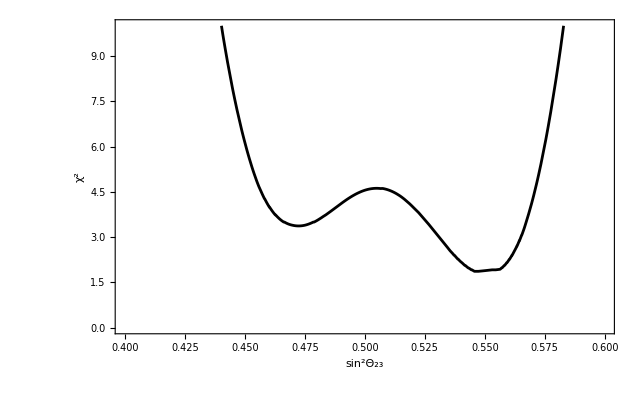

```mathematica
Plot[
Min[
Min[
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,360-ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio],
chisqtilde[{"T23","T13","DCP","T12"},{s23sq,s13sq,ArcCos[cosdcptm1[s23sq,s13sq]]/Pi*180,s12sqtm1[s13sq]},nufitfintio]
] /. s13sq-> # &/@ Range[0.02,0.025,.00005]
]
,
{s23sq,0.4,0.6},
Frame->True,
PlotRange->{{0.4,0.6},{0,10}},
PlotStyle->Black,
FrameLabel->{"sin^2Θ_23","χ^2"},
FrameStyle->Directive[Black,FontSize->20,FontFamily-> Times],
ImageSize->640
]
```